```mathematica
protocolSelect=.
protocolSelect[varName_String]:=Module[{check},check=Select[protocol,StringContainsQ[Keys[#],varName]&]
;If[check=={},Nothing,check]]

strContQ=.
strContQ[v_,t_]:=StringContainsQ[v[[1]],#]&/@t

stringFix=Import["https://github.com/Carl-Firle/effects-of-mask-wearing-on-human-particle-formation/raw/refs/heads/main/methods/stringFix_for_protocol.m"];

dProtocolImport=.
dProtocolImport[filename_String]:=Module[{dProtocol,dProtocolRepl,timeline,var},dProtocol=Import[urlHead ~~filename]
;dProtocol=StringReplace[dProtocol,stringFix]
;dProtocolRepl=Select[StringSplit[dProtocol," --- "],StringContainsQ[#,{"comment***"~~__~~"->"}]&]
;dProtocolRepl=myStringSplit[#,{"comment***"," -> "," :: "}]&/@dProtocolRepl
;dProtocolRepl=(#[[2,2,1]]~~" :: "~~#[[2,1,2]]->#[[2,-1,1]]~~" :: "~~#[[2,-1,2]])&/@dProtocolRepl
;dProtocol=StringReplace[dProtocol,dProtocolRepl]
;protocol=#[[1]]->Quantity[ToExpression[#[[2]]] /1000.,"Seconds"]&/@Select[myStringSplit[dProtocol,{" --- "," :: "}],StringContainsQ[StringJoin[#],"comment***"~~__~~" -> "]==False&]
;protocol=#[[1]]->#[[2]]-Min[Values@protocol]&/@protocol
;startEndTimes=Select[protocol,StringContainsQ[#[[1]],"_start"|"_end"]&]
;startEndTimes[[All,1]]=ToLowerCase/@startEndTimes[[All,1]]
;var=Union[ToLowerCase/@(StringReplace[#,{"_start"->"","_end"->""}]&/@startEndTimes[[All,1]])]
;startEndTimes=GatherBy[startEndTimes,strContQ[#,var]&]
;startEndTimes= GatherBy[#,First]&/@startEndTimes
;startEndTimes=startEndTimes[[All,All,-1]]
;timeline=Range[0,(Values[protocolSelect["end of protocol"]]-Values[protocolSelect["start time"]]) [[1]][[1]]+0.5,.5]
;varNames={"elapsed time [s]"}
;oneTable={timeline}
;"Import successful"]
```

```mathematica
positionInTimeline=.
positionInTimeline[time_]:=Module[{l}
,l=FirstPosition[oneTable[[1]],#][[1]]&@Round[First[time],.5]
]

oneTableAppend=.
oneTableAppend[l_List,vOff_:Missing[],vOn_:1,varName_]:=Module[{pairs,values,ranges,rangePositions,newColumn}
,If[Length[l[[1]]]<=1

,AppendTo[oneTable,l[[2]]];AppendTo[varNames,varName];"no values for "~~varName

,pairs =l[[2]]
;values=l[[1]]
;ranges=values[[{#[[1]],#[[2]]}]][[All,2]]&/@pairs
;rangePositions=Map[positionInTimeline,ranges,{2}]
;newColumn=Table[vOff,Length[oneTable[[1]]]]
;(newColumn[[#1;;#2]]=Table[vOn,Length[newColumn[[#1;;#2]]]])&@@@rangePositions
;AppendTo[varNames,varName]
;AppendTo[oneTable,newColumn]]]
```

```mathematica
synchronize=.
synchronize[l_List,timePosition_Integer,timeStampName_]:=Module[{l2,endTrue}
,l2=l
;endTrue=StringContainsQ[ToLowerCase[timeStampName]~~"_end",Flatten[startEndTimes][[All,1]]]
;Which[endTrue===True
,l2[[All,timePosition]]=Map[Round[UnitConvert[timeStampName~~"_end"/. protocol,"Seconds"]-Quantity[(Max[l[[All,timePosition]]]-#),"Seconds"],.5]&,l2[[All,timePosition]]]
,endTrue===False
,l2[[All,timePosition]]=Map[Round[UnitConvert[timeStampName~~"_start"/. protocol,"Seconds"]+Quantity[(#-Min[l[[All,timePosition]]]),"Seconds"],.5]&,l2[[All,timePosition]]]
,True
,Nothing];
l2]
```

```mathematica
descrDataProtocolImport=.
descrDataProtocolImport[]:=Module[{descrDataProtocolPos,temp,newVarNames,newColumn},
descrDataProtocolPos=(Flatten[Position[protocol,protocolSelect["yearOfBirth"][[1]]]][[1]];;-2)
;temp=protocol[[descrDataProtocolPos]]
;temp=StringSplit[#,"***"]&/@temp[[All,1]]
;newVarNames=temp[[All,1]]
;newColumn=PadRight[{#},Length[oneTable[[1]]],"n.a."]&/@temp[[All,2]]
;AppendTo[oneTable,#]&/@newColumn
;AppendTo[varNames,newVarNames]
;
]

singlePointsImport=.
singlePointsImport[l_List]:=Module[{temp,newVarNames,timepoints,newColumn},
temp=protocolSelect[#]&/@l;
temp=GroupBy[temp,#[[1,1]]&];
newVarNames=Keys[temp];
temp=Flatten[Values[temp],1];
temp[[All,All,2]]=Map[positionInTimeline,temp[[All,All,2]],{2}];
temp=Map[(newColumn=Table["n.a.",Length[oneTable[[1]]]];
newColumn=ReplacePart[newColumn,Map[Reverse,#]];
AppendTo[oneTable,newColumn])&
,temp,{1}][[-1]];
AppendTo[varNames,StringSplit[#,"***"][[1]]&/@newVarNames];
]

(*singlePointsImport[{"mask_order","subject_in_position","subject_exits"}]*)

windowsTimesImport=.
windowsTimesImport[]:=Module[{temp,timepoints,rangePositions,newColumn},
temp=Select[protocol,StringContainsQ[
#[[1]],"window"]&]
;timepoints=GatherBy[temp,#[[1]]&]
;timepoints=If[Length[#1]==Length[#2],Transpose[{#1,#2}],ConstantArray["n.a.",Length[oneTable[[1]]]]]&@@timepoints
;rangePositions=Map[positionInTimeline,timepoints[[All,All,2]],{2}]
;newColumn=Table["closed",Length[oneTable[[1]]]]
;(newColumn[[#1;;#2]]=Table["open",Length[newColumn[[#1;;#2]]]])&@@@rangePositions
;AppendTo[varNames,"window"]
;AppendTo[oneTable,newColumn];]


doorTimesImport=.
doorTimesImport[]:=Module[{temp,timepoints,orderPositions,doorTimes,rangePositions,newColumn},
temp=Select[protocol,StringContainsQ[
#[[1]],"door"]&]
;temp=Append[temp,"door_cabin_exit_closed"->(("end of protocol" /. protocol)-Quantity[.5,"Seconds"])]
;timepoints=GatherBy[temp,StringReplace[#[[1]],{"_start"->"","_end"->""}]&]
;doorTimes=GroupBy[timepoints,StringReplace[#[[1,1]],{"_open"->"","_closed"->""}]&]
;timepoints=If[Equal@@(Length/@#),Transpose[#],#]&/@doorTimes
;rangePositions=Map[positionInTimeline,timepoints[[All,All,All,2]],{3}]
;newColumn=Table[Table["n.a.",Length[oneTable[[1]]]],Length[timepoints]]
;Table[(newColumn[[i,#1;;#2]]="open")&@@@rangePositions[[i]],{i,Length[rangePositions]}]
;AppendTo[oneTable,#]&/@newColumn
;AppendTo[varNames,#]&/@(Keys[doorTimes])
]

airCleanerTimesImport=.
airCleanerTimesImport[]:=Module[{temp,timepoints,orderPositions},
temp=Select[protocol,StringContainsQ[
#[[1]],"airCleaner"]&]
;timepoints=GatherBy[temp,StringReplace[#[[1]],{"_start"->"","_end"->""}]&]
;orderPositions=PositionIndex[#[[All,1]]]&/@timepoints
;temp=If[Length[#]==2,If[Length[#[[1]]]==Length[#[[2]]],Transpose[{#[[1]],#[[2]]}],ConstantArray["off",Length[oneTable[[1]]]]],ConstantArray["off",Length[oneTable[[1]]]]]&/@orderPositions
;temp=Transpose[{timepoints,temp}]
;oneTableAppend[#,"off","on",StringReplace[#[[1,1,1]],{"_start"->"","_end"->""}]]&/@temp
]

measurementTimesImport=.
measurementTimesImport[]:=Module[{temp,timepoints,values,rangePositions,newColumn,valueRangePositionList}
,temp=Select[protocol,StringContainsQ[
#[[1]],"measurement"]&]
;temp=StringSplit[#[[1]],"***"]->#[[2]]&/@Normal[temp]
;timepoints=GatherBy[temp,#[[1,1]]&]
;timepoints=(Select[#,StringContainsQ[#[[1,1]],{"_start","_end"}]&]&/@timepoints) /. ({}->Nothing)
;temp=If[Length[#[[1]]]==Length[#[[2]]],Transpose[#],Transpose[{#[[1]],Append[#[[1]][[2;;-1]],{"measurement_end"}->("end of protocol"/.protocol)-Quantity[1,"Seconds"]]}]]&@timepoints
;values=StringRiffle/@temp[[All,1,1]][[All,2;;-1]]
;rangePositions=Map[positionInTimeline,temp[[All,All,-1]],{2}]
;newColumn=Table["n.a.",Length[oneTable[[1]]]]
;valueRangePositionList=Transpose[{values,rangePositions}]
;(newColumn[[#2[[1]];;#2[[2]]]]=Table[#1,Length[newColumn[[#2[[1]];;#2[[2]]]]]])&@@@valueRangePositionList
;AppendTo[varNames,"measurement task"]
;AppendTo[oneTable,newColumn]
]

measurementCountdownImport=.
measurementCountdownImport[]:=Module[{temp,tempStart,tempEnd,countdownTime,rangePositions,newColumn}
,temp=Select[protocol,StringContainsQ[
#[[1]],{"countdown"}]&]
;tempStart=StringSplit[#[[1]],"***"]->#[[2]]&/@temp
;tempEnd=(StringReplace[#[[1]],"start"->"end"]->(#[[2]]+(countdownTime=Quantity[ToExpression[#[[1,2]]],"Minutes"])))&/@tempStart
;temp=Transpose[{tempStart,tempEnd}]
;rangePositions=Map[positionInTimeline,temp[[All,All,-1]],{2}]
;newColumn=Table["n.a.",Length[oneTable[[1]]]]
;(newColumn[[#1;;#2]]=Range[(#2-#1)/2,0,-.5])&@@@rangePositions
;AppendTo[varNames,"countdown [s]"]
;AppendTo[oneTable,newColumn]
]

loadTimesImport=.
loadTimesImport[]:=Module[{temp,timepoints,orderPositions,search,startTimes,endTimes,periods,loadValues,loadTimes,valueRangePositionList,newColumn},
temp=Select[protocol,StringContainsQ[
#[[1]],{"load_start","load_total","measurement_end"}]&]
;search=Union[Select[temp,StringContainsQ[#[[1]],"load_start"]&][[All,1]]]
;startTimes=Flatten[(Position[temp,#]&/@search)[[All,All,1]]]
;endTimes=(Position[temp,"measurement_end"])[[All,1]]
;periods=If[Length[startTimes]==Length[endTimes],Transpose[{startTimes,endTimes}],"load periods are not determined"]
;temp=temp[[#1;;#2]]&@@@periods
;temp=Map[StringSplit[#[[1]],"***"]->#[[2]]&,Partition[#,2,1],{2}]&/@temp;
;loadValues=temp[[1,All,1,1,2]]
;loadTimes=Map[positionInTimeline,temp[[1,All,All,2]],{2}]
;valueRangePositionList=Transpose[{loadValues,loadTimes}]
;newColumn=Table["n.a.",Length[oneTable[[1]]]]
;(newColumn[[#2[[1]];;#2[[2]]]]=Table[#1,Length[newColumn[[#2[[1]];;#2[[2]]]]]])&@@@valueRangePositionList
;AppendTo[varNames,"load of exercise [Watt]"]
;AppendTo[oneTable,newColumn]
]
```

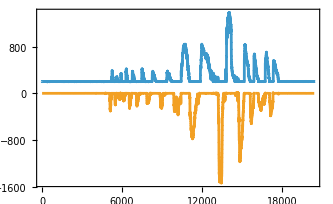
```mathematica
dPexaImport=.
dPexaImport[filename_String,asName_String]:=
Module[{dPexa,dPexaVarNames,dPexaValues,dPexaSync,dPexaSyncMeans,dPexaErrors,newColumn}
,dPexa=Import[urlHead ~~filename]
;dPexa=myStringSplit[dPexa,{"\n","\t"}]
;dPexaVarNames=asName~~"_"~~#&/@(StringReplace[#,{"counts/l"->"1/L","[n]"->"[1]","°C"->"Celsius","%"->"percent","Volume ml]"->"Volume [ml]"}]&/@dPexa[[1]])[[2;;-1]]
;dPexaValues=dPexa[[2;;-15]]
;dPexaValues[[All,1]]=myUnixTime[#]&/@dPexaValues[[All,1]]
;dPexaSync=synchronize[dPexaValues,1,asName]
;dPexaSyncMeans=Map[Mean[ToExpression[#]/. Null->Nothing]&,(Transpose[#]&/@GatherBy[dPexaSync,First])[[All,2;;-1]],{2}] /.( (Mean[{}])->"n.a.")
;
dPexaSyncMeans=myFlatten[Transpose[{Union@dPexaSync[[All,1]],dPexaSyncMeans}],1]
;dPexaErrors=Map[If[NumberQ[#],Around[#,#.1],#]&,dPexaSyncMeans[[All,3;;19]],{2}]
;
dPexaSyncMeans[[All,3;;19]]=dPexaErrors;(*error of 10 %, compare -Graphics-*)
;dPexaSyncMeans[[All,2]]=dPexaSyncMeans[[All,2]]-200
(*there is a constant circuit flow in PExA with 250 ml/s. That shifts the "Exhale Airflow" but not the "Inhale Airflow"! PExA output for "Inhale Exhale Airflow [ml/s]" is misleading! The shift is constantly 200 ml/s not 250 ml/s. See also: https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20251127-01_rip_spiro/rip-spiro-cal.nbhttps://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20251127-01_rip_spiro/rip-spiro-cal.nbNonehttps://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2024_effects-mask-wearing/20251127-01_rip_spiro/rip-spiro-cal.nbHyperlinkActionRecycledHyperlinkActive
-Graphics-
*)
;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[dPexaSyncMeans[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,positionInTimeline[#[[1]]]->#[[2;;-1]]&/@dPexaSyncMeans]
;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,dPexaVarNames[[2;;-1]]]
;
]
```

```mathematica
(*Device specification Grimm 11-Dhttps://grimm-aerosol.ca/data/documents/Grimm-11-D-Datasheet.pdfNonehttps://grimm-aerosol.ca/data/documents/Grimm-11-D-Datasheet.pdfHyperlinkActionRecycledHyperlinkActive*)

dGrimmImport=.
dGrimmImport[filename_String,asName_String]:=Module[{dGrimm,dGrimmVarNames,model,unit,rowVarNames,rowStartData,newColumn}
,dGrimm=Import[urlHead ~~filename,"Text"]
;dGrimm=myStringSplit[StringReplace[dGrimm,","->"."],{"\n","\t"}]
;model=dGrimm[[5,1]]
;unit=Which[StringContainsQ[dGrimm[[9,1]],"ug/m3"],"ug/m3",StringContainsQ[dGrimm[[9,1]],"counts/liter"]||StringContainsQ[dGrimm[[9,1]],"1/l"],"1/L"]
;If[StringContainsQ[model,"11-D"],rowVarNames=15; rowStartData=16,rowVarNames=14; rowStartData=15]

;dGrimmVarNames=asName~~"_"~~#~~" ["~~unit~~"]"&/@dGrimm[[rowVarNames]]
;dGrimm[[rowStartData;;-1]]=Flatten[{UnixTime[FromDateString[#[[1]],{"Day",".","Month",".","Year"," ","Time"}]],ToExpression[#[[2;;-1]]]}]&/@dGrimm[[rowStartData;;-1]]

;dGrimm=synchronize[dGrimm[[rowStartData;;-1]],1,asName]
;dGrimm=myFlatten[Transpose[{dGrimm[[All,1]],Map[Around[#,#.1]&,(dGrimm[[All,2;;-1]]),{2}]}] ,1] (*error of 10 %, compare -Graphics-*)

;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[dGrimm[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,positionInTimeline[#[[1]]]->#[[2;;-1]]&/@dGrimm]

;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,dGrimmVarNames[[2;;-1]]]
;
]
```

```mathematica
(*data sheet https://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdf and statementhttps://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdfNonehttps://sensirion.com/media/documents/8600FF88/64A3B8D6/Sensirion_PM_Sensors_Datasheet_SPS30.pdfHyperlinkActionRecycledHyperlinkActive and precision
 https://sensirion.com/resource/application_note/pm/sensor_specificationhttps://sensirion.com/resource/application_note/pm/sensor_specificationNonehttps://sensirion.com/resource/application_note/pm/sensor_specificationHyperlinkActionRecycledHyperlinkActive*)

errorMassConcSensirionLowPM=.
errorMassConcSensirionLowPM[n_Real]:=Which[0<n<=100,Around[n,n .05 + 5],100<n<=1000,Around[n,n 0.10],True,n]

errorMassConcSensirionHighPM=.
errorMassConcSensirionHighPM[n_Real]:=Which[0<n<=100,Around[n,25],100<n<=1000,Around[n,n 0.25],True,n]

errorNumConcSensirionLowPM=.
errorNumConcSensirionLowPM[n_Real]:=Which[n<=1000,Around[n,100],1000<n<=3000,Around[n,n 0.10],True,n]

errorNumConcSensirionHighPM=.
errorNumConcSensirionHighPM[n_Real]:=Which[n<=1000,Around[n,250],1000<n<=3000,Around[n,n 0.25],True,n]

errorSensirion=.
errorSensirion[l_List/;Length[l]==4]:={errorMassConcSensirionLowPM[#[[1]]],errorMassConcSensirionLowPM[#[[2]]]-errorMassConcSensirionLowPM[#[[1]]],errorMassConcSensirionHighPM[#[[3]]]-errorMassConcSensirionLowPM[#[[2]]],errorMassConcSensirionHighPM[#[[4]]]-errorMassConcSensirionHighPM[#[[3]]]}&@l

errorSensirion[l_List/;Length[l]==5]:=
{errorNumConcSensirionLowPM[#[[1]]],errorNumConcSensirionLowPM[#[[2]]]-errorNumConcSensirionLowPM[#[[1]]],errorNumConcSensirionLowPM[#[[3]]]-errorNumConcSensirionLowPM[#[[2]]],errorNumConcSensirionHighPM[#[[4]]]-errorNumConcSensirionLowPM[#[[3]]],errorNumConcSensirionHighPM[#[[5]]]-errorNumConcSensirionHighPM[#[[4]]]}&@l

dSensirionImport=.
dSensirionImport[filename_String,asName_String]:=Module[{dSensirion,dSensirionVarNames,dSensirionSync,sensirionPositionList,sensirionVarNamesMassNum,id,dErrorSensirion,newColumn},

dSensirion=Import[urlHead ~~filename,"Text"];

dSensirion=myStringSplit[dSensirion,{"\n","\t"}]
;dSensirion[[11;;-1]]=Flatten[{ToExpression[#[[1]]],ToExpression[#[[3;;-1]]]}]&/@dSensirion[[11;;-1]]
;dSensirionVarNames=Delete[dSensirion[[10]],2]

;dSensirionSync=synchronize[dSensirion[[11;;-1]],1,asName]
;
dSensirionSync=(Transpose[If[Length[#]>=2,#/.(Null->Nothing),#]&/@Union/@Transpose[#]]&/@GatherBy[dSensirionSync,First])[[All,1]]

;
sensirionPositionList=Map[Position[dSensirionVarNames,#][[1,1]]&,sensirionVarNamesMassNum=SplitBy[(Select[dSensirionVarNames,StringContainsQ[#,Union[Last[StringSplit[#,"_"]]&/@Rest@dSensirionVarNames]]&&StringContainsQ[#,"TypPartSize"]==False&]),StringContainsQ[#,"Mass"]&],{2}]
;
sensirionVarNamesMassNum=(id=StringTake[#,-5];StringJoin[Flatten[{"AS_",id,"_",StringSplit[#,"_"][[1;;2]]," [",If[StringContainsQ[#,"Mass"],"ug/m3","1/cm3"],"]"}]])&/@Flatten[sensirionVarNamesMassNum]

;
dErrorSensirion=Map[If[Union[#]!={Null},errorSensirion[# ],# /. (Null->"n.a.")]&,dSensirionSync[[All,First[#];;Last[#]]]&/@sensirionPositionList,{2}];
dErrorSensirion=myFlatten[Transpose[{dSensirionSync[[All,1]],Transpose[dErrorSensirion]}],1]

;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[dErrorSensirion[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,positionInTimeline[#[[1]]]->#[[2;;-1]]&/@dErrorSensirion]
;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,sensirionVarNamesMassNum]
]
```

```mathematica
(*Device specification 2435https://static.testo.com/image/upload/HQ/testo-435-data-sheet.pdfNonehttps://static.testo.com/image/upload/HQ/testo-435-data-sheet.pdfHyperlinkActionRecycledHyperlinkActive*)

testoCO2=.
testoCO2[v_Real]:=Module[{},Which[0<=v<=5000,Around[v,75+0.03*v],5001<=v<=10000,Around[v,150+0.05*v],True,"not in measurement range"]]

testoPressure=.
testoPressure[v_Real]:=Module[{},
Around[v,10]
]

testoTemperature=.
testoTemperature[v_Real]:=Module[{},
Around[v,0.3]
]

testoHumidity=.
testoHumidity[v_Real]:=Module[{},
Around[v,2]
]

dtestoImport=.
dtestoImport[filename_String]:= Module[{dtesto,varNamesTesto}
,dtesto=Import[urlHead ~~filename,"Text"]
;dtesto=myStringSplit[StringReplace[dtesto,","->"."],{"\n",";"}]
;varNamesTesto="testo435_"~~#&/@(Prepend[StringReplace[dtesto[[1]][[4;;-1]],{"\""->"","%rF"->"room humidity [percent]","[ppm] CO2"->"CO2 [ppm]","mbar"->"atmospheric pressure [mbar]","°C"->"temperature [Celsius]"}],"time"])
;dtesto= Flatten[{UnixTime[FromDateString[#[[2]]~~ " " ~~ #[[3]]]],ToExpression[#[[4;;-1]]]}]&/@dtesto[[2;;-2]]
;dtesto[[All,2]]=testoCO2/@dtesto[[All,2]]
;dtesto[[All,3]]=testoPressure/@dtesto[[All,3]]
;dtesto[[All,4]]=testoTemperature/@dtesto[[All,4]]
;dtesto[[All,5]]=testoHumidity/@dtesto[[All,5]]
;dtesto=synchronize[dtesto,1,"roomAirCondition"]
;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[dtesto[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,positionInTimeline[#[[1]]]->#[[2;;-1]]&/@dtesto]
;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,varNamesTesto[[2;;-1]]]
;]
```

```mathematica
dMS30Import=.
dMS30Import[filename_String,deviceName_String]:= Module[{dMS30,varNamesMS30,dMS30sync}
,dMS30= Import[urlHead~~filename]
;dMS30=myStringSplit[dMS30,{"\n",";"}]
;varNamesMS30=(StringReplace[#1~~" ["~~#2~~"]","\""->""]&@@@ReplacePart[Transpose[{dMS30[[3]],dMS30[[5]]}],2->{"time","hh:mm:ss"}])[[3;;-1]]
;dMS30= Flatten[{UnixTime[FromDateString[StringReplace[#[[1]]~~ " " ~~ #[[2]],"\""->""],{"Day","Month","Year","Time"}]],ToExpression[StringReplace[#,","->"."]&/@#[[3;;-1]]]}]&/@dMS30[[9;;-1]]
;dMS30sync=synchronize[dMS30,1,deviceName]
;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[dMS30sync[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,Select[positionInTimeline[#[[1]]]->#[[2;;-1]]&/@dMS30sync,#[[1]]!="NotFound"&]]
;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,varNamesMS30]
;
]
```

```mathematica
dDynamometerImport=.
dDynamometerImport[filename_String,deviceName_String,positionForce_Integer:2]:= Module[{ddynamometer}
,ddynamometer=Import[urlHead~~filename]
;ddynamometer=ddynamometer[[All,{1,positionForce}]]
;ddynamometer =synchronize[Rest[ddynamometer],1,deviceName]
;ddynamometer ={#[[1,1]],Mean[#[[All,2]]]}&/@GatherBy[ddynamometer,First]
;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[ddynamometer[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,Select[positionInTimeline[#[[1]]]->#[[2;;-1]]&/@ddynamometer,#[[1]]!="NotFound"&]]
;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,deviceName<>" force ribcage [N]"]
;
]
```

```mathematica
dPexaImport=.
dPexaImport[filename_String,deviceName_String]:= Module[{dPexa,dPexaVarNames,dPexaValues,dPexaSync,dPexaSyncMeans,dPexaErrors,newColumn}
,dPexa=Import[urlHead ~~filename]
;dPexa=myStringSplit[dPexa,{"\n","\t"}]
;dPexaVarNames=deviceName~~"_"~~#&/@(StringReplace[#,{"counts/l"->"1/L","[n]"->"[1]","°C"->"Celsius","%"->"percent","Volume ml]"->"Volume [ml]"}]&/@dPexa[[1]])[[2;;-1]]
;dPexaValues=dPexa[[2;;-15]]; (*the last 14 values are descriptive data*)
;dPexaValues[[All,1]]=myUnixTime[#]&/@dPexaValues[[All,1]]
;dPexaSync=synchronize[dPexaValues,1,deviceName]
;dPexaSyncMeans=Map[Mean[ToExpression[#]/. Null->Nothing]&,(Transpose[#]&/@GatherBy[dPexaSync,First])[[All,2;;-1]],{2}] /.( (Mean[{}])->"n.a.")
;dPexaSyncMeans=myFlatten[Transpose[{Union@dPexaSync[[All,1]],dPexaSyncMeans}],1]
;dPexaErrors=Map[If[NumberQ[#],Around[#,#.1],#]&,dPexaSyncMeans[[All,4;;20]],{2}]
;
dPexaSyncMeans[[All,4;;20]]=dPexaErrors;(*error of 10 %, compare -Graphics-*)
;newColumn=ConstantArray["n.a.",{Length[oneTable[[1]]],Length[dPexaSyncMeans[[-1]]]-1}]
;newColumn=ReplacePart[newColumn,positionInTimeline[#[[1]]]->#[[2;;-1]]&/@dPexaSyncMeans]
;oneTable=Flatten[{oneTable,Transpose[newColumn]},1]
;AppendTo[varNames,dPexaVarNames]
;
]
```

```mathematica
createTabular=.
createTabular[]:=Module[{temp,varNamesList,quantities}
,Clear[s,L,l,ml,ng,ug,cm3,m3,Watt,ppm,mbar,Celsius,percent,n]
;varNamesList=StringReplace[#,"[N]"->"[n]"]&/@Flatten[varNames];quantities=ToExpression[Flatten[StringCases[#,"["~~a__~~"]"->a]&/@varNamesList]] /. {s->"Seconds",L->"Liters",l->"Liters",ml->"Milliliters",ng->"nanogram",ug->"Micrograms",cm3->("Centimeters"^3),m3->("Meters"^3),Watt->"Watts",ppm->"PartsPerMillion",mbar->"Millibars",Celsius->"DegreesCelsius",percent->"Percent",n->"Newtons"}
;temp=oneTable/. "n.a."->Missing[]
;temp=Table[temp[[i]]=Quantity[#,quantities[[i]]]&/@temp[[i]],{i,Length[quantities]}]
;

oneTableCSV=Map[Which[Head[#]===Around,myAroundString[#],NumberQ[#],#,True,StringJoin[#]]&,Transpose[oneTable]/. "n.a."->"",{2}]
;oneTableCSV=Prepend[oneTableCSV,Flatten[varNames]]
;Export[exPath~~"data_"~~StringSplit[urlHead,"/"][[-1]]~~".csv",oneTableCSV]
;oneTableTab=ToTabular[Transpose[temp],"Rows",<|"ColumnKeys"->Flatten[varNames]|>]
;Export[exPath~~"data_"~~StringSplit[urlHead,"/"][[-1]]~~".m",oneTableTab]
]
```